### 3-cycle, all edges the same color

#### Cone of concentration matrices

```mathematica
numVar=4;
numTrials=1000;
listCoef=RandomInteger[1000,{numTrials,numVar}];
KEdges={{l1,l4,l4},{l4,l2,l4},{l4,l4,l3}};
LEdges={l1,l2,l3,l4};
estRankEdges={};
solLEdges={};
For[i=1,i<numTrials+1,i++,sol=SemidefiniteOptimization[listCoef[[i]].LEdges,{KEdges(\[VectorGreaterEqual])_Length[KEdges] 0,Tr[KEdges]==1},LEdges];
AppendTo[solLEdges,sol];
estK=KEdges/.sol;estRankK=MatrixRank[N[estK],Tolerance->10^(-7)];AppendTo[estRankEdges,estRankK]]
Counts[estRankEdges]
```

<|1→604,2→396|>

```mathematica
solLEdgesRk1=Flatten[Position[estRankEdges,1]];
solLEdgesRk2=Flatten[Position[estRankEdges,2]];
solLEdgesMat=List@@@solLEdges[[;;,{1,2,4},2]];
solLEdgesMatRk1=List@@@solLEdges[[solLEdgesRk1,{1,2,4},2]];
solLEdgesMatRk2=List@@@solLEdges[[solLEdgesRk2,{1,2,4},2]];
```

```mathematica
ListPointPlot3D[{solLEdgesMatRk1,solLEdgesMatRk2}]
```

-Graphics3D-

```mathematica
ListPointPlot3D[solLEdgesMatRk1]
```

-Graphics3D-

```mathematica
plotKG=ConvexHullMesh[solLEdgesMat,MeshCellStyle->{2->Opacity[.5,Red]}]
```

-Graphics3D-

#### Cone of sufficient statistics

```mathematica
numTrials=1000;
rk=2;
statsListRk2={};
For[i=1,i<numTrials+1,i++,
X=RandomReal[{-10,10},{3,rk,numTrials}];
S=X[[;;,;;,i]] .Transpose[X[[;;,;;,i]]];
a=Tr[S];
SCompact=1/a S;
t1=SCompact[[1,1]];
t2=SCompact[[2,2]];
t4=SCompact[[1,2]]+SCompact[[1,3]]+SCompact[[2,3]];
stats={t1,t2,t4};
AppendTo[statsListRk2,stats]]
rk=3;
statsListRk3={};
For[i=1,i<numTrials+1,i++,
X=RandomReal[{-10,10},{3,rk,numTrials}];
S=X[[;;,;;,i]] .Transpose[X[[;;,;;,i]]];
a=Tr[S];
SCompact=1/a S;
t1=SCompact[[1,1]];
t2=SCompact[[2,2]];
t4=SCompact[[1,2]]+SCompact[[1,3]]+SCompact[[2,3]];
stats={t1,t2,t4};
AppendTo[statsListRk3,stats]]
```

```mathematica
ListPointPlot3D[{statsListRk3,statsListRk2}]
```

-Graphics3D-

```mathematica
plotCG=ConvexHullMesh[Join[statsListRk3,statsListRk2]]
```

-Graphics3D-

```mathematica
Show[plotKG,HighlightMesh[plotCG,Style[2,Opacity[0.5]]]]
```

-Graphics3D-

```mathematica
numVar=4;
numTrials=1000;
listCoef=RandomInteger[1000,{numTrials,numVar}];
TEdges={T1,T2,T3,T4};
solTEdges={};
For[i=1,i<numTrials+1,i++,sol=LinearOptimization[-listCoef[[i]].TEdges,{List@@@solLEdges[[;;,;;,2]].TEdges\[VectorGreaterEqual]0,T1+T2+T3==1},TEdges];
AppendTo[solTEdges,sol]]
```

```mathematica
solTEdgesMat=List@@@solTEdges[[;;,{1,2,4},2]];
```

```mathematica
plotCGAlt=ConvexHullMesh[solTEdgesMat,MeshCellStyle->{2->Opacity[.5,Blue]}]
```

-Graphics3D-

```mathematica
Show[plotKG,plotCGAlt]
```

-Graphics3D-

```mathematica
G1=16*T1^4+32*T1^3*T2+48*T1^2*T2^2+32*T1*T2^3+16*T2^4+64*T1^2*T2*T4+64*T1*T2^2*T4+8*T1^2*T4^2+8*T1*T2*T4^2+8*T2^2*T4^2+T4^4-32*T1^3-32*T2^3-64*T1*T2*T4-8*T1*T4^2-8*T2*T4^2+16*T1^2-32*T1*T2+16*T2^2;
```

```mathematica
plotG1=ContourPlot3D[G1,{T1,-1,1},{T2,-1,1},{T4,-1,1}]
```

-Graphics3D-

```mathematica
Show[plotCGAlt, plotG1]
```

-Graphics3D-

```mathematica
Show[plotCG, plotG1]
```

-Graphics3D-

```mathematica
statsListAllEdges=Join[statsListRk3,statsListRk2]
```

{{0.282087,0.326499,-0.425154},{0.166615,0.436323,0.124492},{0.316636,0.30638,0.220102},1994,{0.145583,0.552627,0.33024},{0.247837,0.631066,-0.263136},{0.596633,0.194835,0.385256}}
 |  |  |  |

```mathematica
evalEdges={};
```

```mathematica
For[i=1,i<Length[statsListAllEdges]+1,i++,eval=G1/.{T1->statsListAllEdges[[i,1]],T2->statsListAllEdges[[i,2]],T4->statsListAllEdges[[i,3]]};
AppendTo[evalEdges,eval]]
```

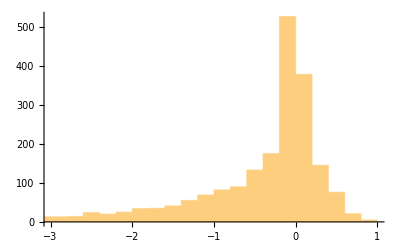

```mathematica
Histogram[%315]
```

```mathematica
EvalPtsEdges=Transpose[Append[Transpose[statsListAllEdges],evalEdges]];
```

```mathematica
PositionPositivePts=Position[evalEdges,_?Positive];
```

```mathematica
PositionNegativePts=Position[evalEdges,_?Negative];
```

```mathematica
statsListAllEdgesPos=statsListAllEdges[[Flatten[PositionPositivePts],;;]];
```

```mathematica
statsListAllEdgesNeg=statsListAllEdges[[Flatten[PositionNegativePts],;;]];
```

```mathematica
ListPointPlot3D[{statsListAllEdgesPos,statsListAllEdgesNeg}]
```

-Graphics3D-

```mathematica
CHEdgesPos=ConvexHullMesh[statsListAllEdgesPos,MeshCellStyle->{2->Opacity[.5,Red]}];
```

```mathematica
CHEdgesNeg=ConvexHullMesh[statsListAllEdgesNeg,MeshCellStyle->{2->Opacity[.5,Blue]}];
```

```mathematica
Show[CHEdgesPos,CHEdgesNeg]
```

-Graphics3D-

### 3-cycle, all vertices the same color

#### Cone of concentration matrices

```mathematica
numVar=4;
numTrials=1000;
listCoef=RandomInteger[1000,{numTrials,numVar}];
KVertices={{l1,l2,l3},{l2,l1,l4},{l3,l4,l1}};
LVertices={l1,l2,l3,l4};
estRankVertices={};
solLVertices={};
For[i=1,i<numTrials+1,i++,sol=SemidefiniteOptimization[listCoef[[i]].LVertices,{KVertices(\[VectorGreaterEqual])_Length[KVertices] 0,Tr[KVertices]==1},LVertices];
AppendTo[solLVertices,sol];
estK=KVertices/.sol;estRankK=MatrixRank[N[estK],Tolerance->10^(-7)];AppendTo[estRankVertices,estRankK]]
Counts[estRankVertices]
```

<|1→621,2→379|>

```mathematica
solLVerticesRk1=Flatten[Position[estRankVertices,1]];
solLVerticesRk2=Flatten[Position[estRankVertices,2]];
solLVerticesMat=List@@@solLVertices[[;;,{2,3,4},2]];
solLVerticesMatRk1=List@@@solLVertices[[solLVerticesRk1,{2,3,4},2]];
solLVerticesMatRk2=List@@@solLVertices[[solLVerticesRk2,{2,3,4},2]];
```

```mathematica
ListPointPlot3D[{solLVerticesMatRk1,solLVerticesMatRk2}]
```

-Graphics3D-

```mathematica
ListPointPlot3D[solLVerticesMatRk1]
```

-Graphics3D-

```mathematica
plotKGVertices=ConvexHullMesh[solLVerticesMat,MeshCellStyle->{2->Opacity[.5,Red]}]
```

-Graphics3D-

#### Cone of sufficient statistics

```mathematica
numTrials=1000;
rk=2;
statsListVerticesRk2={};
For[i=1,i<numTrials+1,i++,
X=RandomReal[{-10,10},{3,rk,numTrials}];
S=X[[;;,;;,i]] .Transpose[X[[;;,;;,i]]];
a=Tr[S];
SCompact=1/a S;
t2=SCompact[[1,2]];
t3=SCompact[[1,3]];
t4=SCompact[[2,3]];
stats={t2,t3,t4};
AppendTo[statsListVerticesRk2,stats]]
rk=3;
statsListVerticesRk3={};
For[i=1,i<numTrials+1,i++,
X=RandomReal[{-10,10},{3,rk,numTrials}];
S=X[[;;,;;,i]] .Transpose[X[[;;,;;,i]]];
a=Tr[S];
SCompact=1/a S;
t2=SCompact[[1,2]];
t3=SCompact[[1,3]];
t4=SCompact[[2,3]];
stats={t2,t3,t4};
AppendTo[statsListVerticesRk3,stats]]
```

```mathematica
ListPointPlot3D[{statsListVerticesRk3,statsListVerticesRk2}]
```

-Graphics3D-

```mathematica
plotCGVertices=ConvexHullMesh[Join[statsListVerticesRk3,statsListVerticesRk2]]
```

-Graphics3D-

```mathematica
Show[plotKGVertices,HighlightMesh[plotCGVertices,Style[2,Opacity[0.5]]]]
```

-Graphics3D-

```mathematica
G1Vertices=3*T2^2*T3^2+3*T2^2*T4^2+3*T3^2*T4^2-2*T2*T3*T4
```

3 T2^2 T3^2-2 T2 T3 T4+3 T2^2 T4^2+3 T3^2 T4^2

```mathematica
plotG1Vertices=ContourPlot3D[G1Vertices,{T2,-1,1},{T3,-1,1},{T4,-1,1}]
```

-Graphics3D-

```mathematica
Show[HighlightMesh[plotCGVertices,Style[2,Opacity[0.5]]], plotG1Vertices]
```

-Graphics3D-

### Other

```mathematica
f[x1_,x2_,x3_,x4_]:=x1 x2 x3 -x1 x4^2-x2 x4^2-x3 x4^2+2x4^3
```

```mathematica
T={t1,t2,t3,t4,t5,t6,t7,t8,t9,t10,t11,t12};
```

```mathematica
K={{l1,l6,0,l9,l10},{l6,l2,l7,0,l11},{0,l7,l3,l8,l12},{l9,0,l8,l4,0},{l10,l11,l12,0,l5}}
```

```mathematica
M=Table[Subscript[x, i,j],{i,1,3},{j,1,3}]
```

{{x_(1,1),x_(1,2),x_(1,3)},{x_(2,1),x_(2,2),x_(2,3)},{x_(3,1),x_(3,2),x_(3,3)}}

```mathematica
MatrixForm[M]
```

(x_(1,1) | x_(1,2) | x_(1,3)
x_(2,1) | x_(2,2) | x_(2,3)
x_(3,1) | x_(3,2) | x_(3,3))

```mathematica
S=M Transpose[M]
```

{{x_(1,1)^2,x_(1,2) x_(2,1),x_(1,3) x_(3,1)},{x_(1,2) x_(2,1),x_(2,2)^2,x_(2,3) x_(3,2)},{x_(1,3) x_(3,1),x_(2,3) x_(3,2),x_(3,3)^2}}

```mathematica
MatrixForm[S]
```

(x_(1,1)^2 | x_(1,2) x_(2,1) | x_(1,3) x_(3,1)
x_(1,2) x_(2,1) | x_(2,2)^2 | x_(2,3) x_(3,2)
x_(1,3) x_(3,1) | x_(2,3) x_(3,2) | x_(3,3)^2)

```mathematica
X={{x1,x2,x3},a{x1,x2,x3},b{x1,x2,x3}}
```

{{x1,x2,x3},{a x1,a x2,a x3},{b x1,b x2,b x3}}

```mathematica
S=X Transpose[X]
```

{{x1^2,a x1 x2,b x1 x3},{a x1 x2,a^2 x2^2,a b x2 x3},{b x1 x3,a b x2 x3,b^2 x3^2}}

```mathematica
Tr[S]
```

x1^2+a^2 x2^2+b^2 x3^2

### Adjugate

```mathematica
M=Table[Subscript[x, i,j],{i,1,2},{j,1,3}]
```

{{x_(1,1),x_(1,2),x_(1,3)},{x_(2,1),x_(2,2),x_(2,3)}}

```mathematica
MatrixForm[M]
```

(x_(1,1) | x_(1,2) | x_(1,3)
x_(2,1) | x_(2,2) | x_(2,3))

```mathematica
S=Transpose[M].M
```

{{x_(1,1)^2+x_(2,1)^2,x_(1,1) x_(1,2)+x_(2,1) x_(2,2),x_(1,1) x_(1,3)+x_(2,1) x_(2,3)},{x_(1,1) x_(1,2)+x_(2,1) x_(2,2),x_(1,2)^2+x_(2,2)^2,x_(1,2) x_(1,3)+x_(2,2) x_(2,3)},{x_(1,1) x_(1,3)+x_(2,1) x_(2,3),x_(1,2) x_(1,3)+x_(2,2) x_(2,3),x_(1,3)^2+x_(2,3)^2}}

```mathematica
MatrixForm[S]
```

(x_(1,1)^2+x_(2,1)^2 | x_(1,1) x_(1,2)+x_(2,1) x_(2,2) | x_(1,1) x_(1,3)+x_(2,1) x_(2,3)
x_(1,1) x_(1,2)+x_(2,1) x_(2,2) | x_(1,2)^2+x_(2,2)^2 | x_(1,2) x_(1,3)+x_(2,2) x_(2,3)
x_(1,1) x_(1,3)+x_(2,1) x_(2,3) | x_(1,2) x_(1,3)+x_(2,2) x_(2,3) | x_(1,3)^2+x_(2,3)^2)

```mathematica
AdjS=Minors[S,2]
```

{{x_(1,2)^2 x_(2,1)^2-2 x_(1,1) x_(1,2) x_(2,1) x_(2,2)+x_(1,1)^2 x_(2,2)^2,x_(1,2) x_(1,3) x_(2,1)^2-x_(1,1) x_(1,3) x_(2,1) x_(2,2)-x_(1,1) x_(1,2) x_(2,1) x_(2,3)+x_(1,1)^2 x_(2,2) x_(2,3),x_(1,2) x_(1,3) x_(2,1) x_(2,2)-x_(1,1) x_(1,3) x_(2,2)^2-x_(1,2)^2 x_(2,1) x_(2,3)+x_(1,1) x_(1,2) x_(2,2) x_(2,3)},{x_(1,2) x_(1,3) x_(2,1)^2-x_(1,1) x_(1,3) x_(2,1) x_(2,2)-x_(1,1) x_(1,2) x_(2,1) x_(2,3)+x_(1,1)^2 x_(2,2) x_(2,3),x_(1,3)^2 x_(2,1)^2-2 x_(1,1) x_(1,3) x_(2,1) x_(2,3)+x_(1,1)^2 x_(2,3)^2,x_(1,3)^2 x_(2,1) x_(2,2)-x_(1,2) x_(1,3) x_(2,1) x_(2,3)-x_(1,1) x_(1,3) x_(2,2) x_(2,3)+x_(1,1) x_(1,2) x_(2,3)^2},{x_(1,2) x_(1,3) x_(2,1) x_(2,2)-x_(1,1) x_(1,3) x_(2,2)^2-x_(1,2)^2 x_(2,1) x_(2,3)+x_(1,1) x_(1,2) x_(2,2) x_(2,3),x_(1,3)^2 x_(2,1) x_(2,2)-x_(1,2) x_(1,3) x_(2,1) x_(2,3)-x_(1,1) x_(1,3) x_(2,2) x_(2,3)+x_(1,1) x_(1,2) x_(2,3)^2,x_(1,3)^2 x_(2,2)^2-2 x_(1,2) x_(1,3) x_(2,2) x_(2,3)+x_(1,2)^2 x_(2,3)^2}}

```mathematica
MatrixForm[%446]
```

```mathematica
({{Subscript[x, 1,2]^2 Subscript[x, 2,1]^2-2 Subscript[x, 1,1] Subscript[x, 1,2] Subscript[x, 2,1] Subscript[x, 2,2]+Subscript[x, 1,1]^2 Subscript[x, 2,2]^2, Subscript[x, 1,2] Subscript[x, 1,3] Subscript[x, 2,1]^2-Subscript[x, 1,1] Subscript[x, 1,3] Subscript[x, 2,1] Subscript[x, 2,2]-Subscript[x, 1,1] Subscript[x, 1,2] Subscript[x, 2,1] Subscript[x, 2,3]+Subscript[x, 1,1]^2 Subscript[x, 2,2] Subscript[x, 2,3], Subscript[x, 1,2] Subscript[x, 1,3] Subscript[x, 2,1] Subscript[x, 2,2]-Subscript[x, 1,1] Subscript[x, 1,3] Subscript[x, 2,2]^2-Subscript[x, 1,2]^2 Subscript[x, 2,1] Subscript[x, 2,3]+Subscript[x, 1,1] Subscript[x, 1,2] Subscript[x, 2,2] Subscript[x, 2,3]}, {Subscript[x, 1,2] Subscript[x, 1,3] Subscript[x, 2,1]^2-Subscript[x, 1,1] Subscript[x, 1,3] Subscript[x, 2,1] Subscript[x, 2,2]-Subscript[x, 1,1] Subscript[x, 1,2] Subscript[x, 2,1] Subscript[x, 2,3]+Subscript[x, 1,1]^2 Subscript[x, 2,2] Subscript[x, 2,3], Subscript[x, 1,3]^2 Subscript[x, 2,1]^2-2 Subscript[x, 1,1] Subscript[x, 1,3] Subscript[x, 2,1] Subscript[x, 2,3]+Subscript[x, 1,1]^2 Subscript[x, 2,3]^2, Subscript[x, 1,3]^2 Subscript[x, 2,1] Subscript[x, 2,2]-Subscript[x, 1,2] Subscript[x, 1,3] Subscript[x, 2,1] Subscript[x, 2,3]-Subscript[x, 1,1] Subscript[x, 1,3] Subscript[x, 2,2] Subscript[x, 2,3]+Subscript[x, 1,1] Subscript[x, 1,2] Subscript[x, 2,3]^2}, {Subscript[x, 1,2] Subscript[x, 1,3] Subscript[x, 2,1] Subscript[x, 2,2]-Subscript[x, 1,1] Subscript[x, 1,3] Subscript[x, 2,2]^2-Subscript[x, 1,2]^2 Subscript[x, 2,1] Subscript[x, 2,3]+Subscript[x, 1,1] Subscript[x, 1,2] Subscript[x, 2,2] Subscript[x, 2,3], Subscript[x, 1,3]^2 Subscript[x, 2,1] Subscript[x, 2,2]-Subscript[x, 1,2] Subscript[x, 1,3] Subscript[x, 2,1] Subscript[x, 2,3]-Subscript[x, 1,1] Subscript[x, 1,3] Subscript[x, 2,2] Subscript[x, 2,3]+Subscript[x, 1,1] Subscript[x, 1,2] Subscript[x, 2,3]^2, Subscript[x, 1,3]^2 Subscript[x, 2,2]^2-2 Subscript[x, 1,2] Subscript[x, 1,3] Subscript[x, 2,2] Subscript[x, 2,3]+Subscript[x, 1,2]^2 Subscript[x, 2,3]^2}})
```

{{x_(1,2)^2 x_(2,1)^2-2 x_(1,1) x_(1,2) x_(2,1) x_(2,2)+x_(1,1)^2 x_(2,2)^2,x_(1,2) x_(1,3) x_(2,1)^2-x_(1,1) x_(1,3) x_(2,1) x_(2,2)-x_(1,1) x_(1,2) x_(2,1) x_(2,3)+x_(1,1)^2 x_(2,2) x_(2,3),x_(1,2) x_(1,3) x_(2,1) x_(2,2)-x_(1,1) x_(1,3) x_(2,2)^2-x_(1,2)^2 x_(2,1) x_(2,3)+x_(1,1) x_(1,2) x_(2,2) x_(2,3)},{x_(1,2) x_(1,3) x_(2,1)^2-x_(1,1) x_(1,3) x_(2,1) x_(2,2)-x_(1,1) x_(1,2) x_(2,1) x_(2,3)+x_(1,1)^2 x_(2,2) x_(2,3),x_(1,3)^2 x_(2,1)^2-2 x_(1,1) x_(1,3) x_(2,1) x_(2,3)+x_(1,1)^2 x_(2,3)^2,x_(1,3)^2 x_(2,1) x_(2,2)-x_(1,2) x_(1,3) x_(2,1) x_(2,3)-x_(1,1) x_(1,3) x_(2,2) x_(2,3)+x_(1,1) x_(1,2) x_(2,3)^2},{x_(1,2) x_(1,3) x_(2,1) x_(2,2)-x_(1,1) x_(1,3) x_(2,2)^2-x_(1,2)^2 x_(2,1) x_(2,3)+x_(1,1) x_(1,2) x_(2,2) x_(2,3),x_(1,3)^2 x_(2,1) x_(2,2)-x_(1,2) x_(1,3) x_(2,1) x_(2,3)-x_(1,1) x_(1,3) x_(2,2) x_(2,3)+x_(1,1) x_(1,2) x_(2,3)^2,x_(1,3)^2 x_(2,2)^2-2 x_(1,2) x_(1,3) x_(2,2) x_(2,3)+x_(1,2)^2 x_(2,3)^2}}

```mathematica
S[[2,2]]S[[3,3]]-S[[2,3]]S[[3,2]]-AdjS[[3,3]]
```

-x_(1,3)^2 x_(2,2)^2+2 x_(1,2) x_(1,3) x_(2,2) x_(2,3)-x_(1,2)^2 x_(2,3)^2-(x_(1,2) x_(1,3)+x_(2,2) x_(2,3))^2+(x_(1,2)^2+x_(2,2)^2) (x_(1,3)^2+x_(2,3)^2)

```mathematica
Simplify[%456]
```

0

```mathematica
Expand[-(Subscript[x, 1,2] Subscript[x, 1,3]+Subscript[x, 2,2] Subscript[x, 2,3])^2+(Subscript[x, 1,2]^2+Subscript[x, 2,2]^2) (Subscript[x, 1,3]^2+Subscript[x, 2,3]^2)]
```

x_(1,3)^2 x_(2,2)^2-2 x_(1,2) x_(1,3) x_(2,2) x_(2,3)+x_(1,2)^2 x_(2,3)^2

```mathematica
Simplify[%452]
```

(x_(1,1)^2+x_(1,3)^2) x_(2,2)^2-2 x_(1,2) x_(2,2) (x_(1,1) x_(2,1)+x_(1,3) x_(2,3))+x_(1,2)^2 (x_(2,1)^2+x_(2,3)^2)

```mathematica
MatrixRank[AdjS]
```

1

### Adjugates

```mathematica
range=100;
numRuns=10000;
numObs=2;
numCoordinates=3;
num=RandomInteger[{-range,range},{numRuns, numObs,numCoordinates}];
den=RandomChoice[Join[-Range[range],Range[range]],{numRuns, numObs,numCoordinates}];
```

```mathematica
sampleList=ConstantArray[0,{numRuns, numObs,numCoordinates}];
```

```mathematica
For[i=1,i<numRuns+1,i++,
For[j=1,j<numObs+1,j++,
For[k=1,k<numCoordinates+1,k++,
sampleList[[i,j,k]]=num[[i,j,k]]/den[[i,j,k]]
]
]
]
```

```mathematica
sampleConcentrationList={};
For[i=1,i<numRuns+1,i++,
AppendTo[sampleConcentrationList, Transpose[sampleList[[i,;;]]].sampleList[[i,;;]]]
]
```

```mathematica
sampleCovarianceList={};
For[i=1,i<numRuns+1,i++,
AppendTo[sampleCovarianceList, Minors[sampleConcentrationList[[i]],2]];
sampleCovarianceList[[i]]=1/Tr[sampleCovarianceList[[i]]]sampleCovarianceList[[i]]
]
```

```mathematica
statsListEdgesFromAdj={};
For[i=1,i<numRuns+1,i++,
t1=sampleCovarianceList[[i,1,1]];
t2=sampleCovarianceList[[i,2,2]];
t4=sampleCovarianceList[[i,1,2]]+sampleCovarianceList[[i,1,3]]+sampleCovarianceList[[i,2,3]];
stats={t1,t2,t4};
AppendTo[statsListEdgesFromAdj,stats]]
```

```mathematica
(*For[i=1,i<numRuns+1,i++,Print[Tr[sampleCovarianceList[[i]]]]]*)
```

```mathematica
numTrueObs=1;
```

```mathematica
numTrue=RandomInteger[{-range,range},{numRuns, numTrueObs,numCoordinates}];
denTrue=RandomChoice[Join[-Range[range],Range[range]],{numRuns, numTrueObs,numCoordinates}];
```

```mathematica
sampleListTrue=ConstantArray[0,{numRuns, numTrueObs,numCoordinates}];
```

```mathematica
For[i=1,i<numRuns+1,i++,
For[j=1,j<numTrueObs+1,j++,
For[k=1,k<numCoordinates+1,k++,
sampleListTrue[[i,j,k]]=numTrue[[i,j,k]]/denTrue[[i,j,k]]
]
]
]
```

```mathematica
sampleTrueCovarianceList={};
For[i=1,i<numRuns+1,i++,
AppendTo[sampleTrueCovarianceList, Transpose[sampleListTrue[[i,;;]]].sampleListTrue[[i,;;]]]
]
```

```mathematica
statsListEdgesTrue={};
For[i=1,i<numRuns+1,i++,
t1=sampleTrueCovarianceList[[i,1,1]];
t2=sampleTrueCovarianceList[[i,2,2]];
t4=sampleTrueCovarianceList[[i,1,2]]+sampleTrueCovarianceList[[i,1,3]]+sampleTrueCovarianceList[[i,2,3]];
stats={t1,t2,t4};
AppendTo[statsListEdgesTrue,stats]]
```

```mathematica
statsListEdgesTrue;
```

```mathematica
trueStatsEdges=ListPointPlot3D[statsListEdgesTrue,PlotStyle->Brown]
```

-Graphics3D-

```mathematica
adjStatsEdges=ListPointPlot3D[statsListEdgesFromAdj,PlotStyle->Blue]
```

-Graphics3D-

```mathematica
Show[trueStatsEdges,adjStatsEdges]
```

-Graphics3D-

```mathematica
RegionMeasure[trueStatsEdges]
```

RegionMeasure::reg: is not a correctly specified region.

RegionMeasure[-Graphics3D-]

```mathematica
statsListVerticesFromAdj={};
For[i=1,i<numRuns+1,i++,
t2=sampleCovarianceList[[i,1,2]];
t3=sampleCovarianceList[[i,1,3]];
t4=sampleCovarianceList[[i,2,3]];
stats={t2,t3,t4};
AppendTo[statsListVerticesFromAdj,stats]]
```

```mathematica
statsListVerticesTrue={};
For[i=1,i<numRuns+1,i++,
t2=sampleTrueCovarianceList[[i,1,2]];
t3=sampleTrueCovarianceList[[i,1,3]];
t4=sampleTrueCovarianceList[[i,2,3]];
stats={t2,t3,t4};
AppendTo[statsListVerticesTrue,stats]]
```

```mathematica
trueStatsVertices=ListPointPlot3D[statsListVerticesTrue,PlotStyle->Red]
```

-Graphics3D-

```mathematica
adjStatsVertices=ListPointPlot3D[statsListVerticesTrue,PlotStyle->Purple]
```

-Graphics3D-

```mathematica
Show[trueStatsVertices,adjStatsVertices]
```

-Graphics3D-

```mathematica
PointCloudToImage3D[points_]:=Block[{ranges,bins,binCounts,transposedBinCounts},ranges=Round[{Min[#],Max[#]}&/@Transpose[points]];
bins=Append[#,0.5]&/@ranges;
binCounts=BinCounts[points,Sequence@@bins];
transposedBinCounts=Reverse[Transpose[binCounts,{3,2,1}],{1,2}];
Blur[ImageAdjust@Image3D[transposedBinCounts],2]]
```

```mathematica
PointCloudToImage3D[adjStatsEdges]
```

Transpose::nmtx: The first two levels of {,} cannot be transposed.

Transpose::permspec: Invalid permutation specification found at position 2 in Transpose[{,},0.5].

BinCounts::vectmat: The first argument is expected to be a vector or matrix.

Transpose::permspec: Invalid permutation specification found at position 2 in Transpose[{1,2,3},BinCounts[Transpose[{,},0.5],]].

Image3D::imgarray: The specified argument Transpose[{1,2,3},BinCounts[Transpose[{,},0.5],]] should be an array of rank 3 or 4 with machine-sized numbers or a list of images of consistent dimension and color space.

ImageAdjust::imginv: Expecting an image or graphics instead of Image3D[Transpose[{1,2,3},BinCounts[Transpose[{,},0.5],]]].

Blur::imginv: Expecting an image or graphics instead of ImageAdjust[Image3D[Transpose[{1,2,3},BinCounts[Transpose[{,},0.5],]]]].

Blur[ImageAdjust[Image3D[Transpose[{1,2,3},BinCounts[Transpose[{-Graphics3D-,-Graphics3D-},0.5],-Graphics3D-]]]],2]